# Superposition continue des ondes

(Impulsion non-périodique ou Paquet d’onde)

```mathematica
Clear["Global`*"]
```

## Paquet d’onde

La distribution spectrale des amplitudes:

```mathematica
Subscript[k, 0]:=2;α:=4;A[k_]=ⅇ^(-α (k-Subscript[k, 0])^2)
```

ⅇ^(-4 (-2+k)^2)

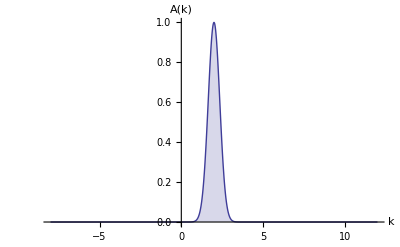

```mathematica
Plot[A[k],{k,Subscript[k, 0]-10,Subscript[k, 0]+10},Filling->Axis,PlotRange->{0,1},AxesLabel->{"k","A(k)"}]
```

Relation de dispersion :

```mathematica
ω[k_]:=k^2
```

Fonction d’onde:

```mathematica
ψ[x_,t_]=∫_(-∞)^∞ A[k] ⅇ^(ⅈ (k x-ω[k] t))ⅆk;
```

```mathematica
Animate[Plot[Re[ψ[x,t]],{x,-10,200},PlotRange->{-1,1},AxesLabel->{"t","Re[ψ(x,t)]"}],{t,0,100,0.01},AnimationRunning->False]
```

Densité de probabilité de présence:

```mathematica
P[x_,t_]=ψ[x,t]ψ[x,t]*;
```

```mathematica
Animate[Plot[P[x,t],{x,-10,200},PlotRange->{-1,1},AxesLabel->{"t","P(x,t)"}],{t,0,100,0.1},AnimationRunning->False]
```

## La relation de réciprocité

### Dans l’ espace de x

```mathematica
t:=0
```

```mathematica
P[x_]=P[x,t];
```

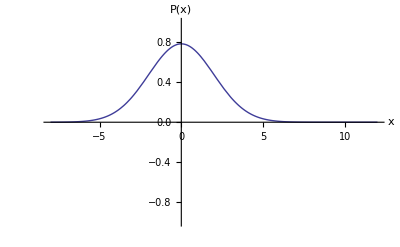

```mathematica
Plot[P[x],{x,Subscript[k, 0]-10,Subscript[k, 0]+10},PlotRange->{-1,1},AxesLabel->{"x","P(x)"}]
```

Densité de probabilité

```mathematica
∫_(-∞)^∞ P[x] ⅆx//N
```

3.9374

Moyenne de x

```mathematica
⟨x⟩=∫_(-∞)^∞ x P[x] ⅆx;
```

Moyenne de x^2

```mathematica
⟨x^2⟩=∫_(-∞)^∞ x^2 P[x]ⅆx;
```

Largeur

```mathematica
Δx=√(⟨x^2⟩-⟨x⟩^2)//N
```

3.96858

### Dans l’ espace de k

```mathematica
P[k_]=A[k]A[k]*;
```

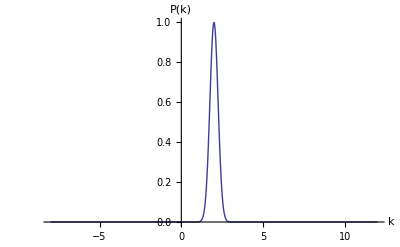

```mathematica
Plot[P[k],{k,Subscript[k, 0]-10,Subscript[k, 0]+10},PlotRange->All,AxesLabel->{"k","P(k)"}]
```

Densité de probabilité

```mathematica
∫_(-∞)^∞ P[k] ⅆk//N
```

0.626657

Moyenne de x

```mathematica
⟨k⟩=∫_(-∞)^∞ k P[k] ⅆk;
```

Moyenne de x^2

```mathematica
⟨k^2⟩=∫_(-∞)^∞ k^2 P[k] ⅆk;
```

Largeur

```mathematica
Δk=√(⟨k^2⟩-⟨k⟩^2)//N
```

0.98742

#### La relation de réciprocité

```mathematica
Δx Δk//N
```

3.91865

## Vitesse

Vitesse de phase (m/s)

```mathematica
Subscript[v, ϕ]=ω[k]/k
```

k

```mathematica
Table[Subscript[v, ϕ],{k,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

Vitesse de groupe (m/s)

```mathematica
Subscript[v, g]=D[ω[k],k]/.k->Subscript[k, 0]
```

4